## HW1- ME634:Turbulence, Spring2017 Prof. Truman, Student:Brad Philipbar

## Part 1:

1A) Derive the two-dimensional small-disturbance equations from Navier-Stokes equations. Carefully explain all assumptions. Explain why the three-dimensional small-disturbance equations have the same form as the 2-D equations.

## Using Cebeci & Bradshaw, if incompressible, equation 2.3.9 (x component) becomes {u,v,w,p} -> {u+u’, v+v’, w+w’,p+p’}

```mathematica
∂u/∂t +∂u'/∂t +(u+u')∂u/∂x+(u+u')∂u'/∂x+(v+v')∂u/∂y+(v+v')∂u'/∂y+(w+w')∂u/∂z+(w+w')∂u'/∂z = -1/ρ ∂p/∂x -1/ρ ∂p'/∂x + ν (∂^2u/∂x^2+∂^2u/∂y^2+∂^2u/∂z^2)+ ν (∂^2u'/∂x^2+∂^2u'/∂y^2+∂^2u'/∂z^2)+fx
```

since all primes are small (they are perturbations) we can ignore the terms with two primes multiplied. And we drop out the part of the equation that is the original 2.3.9 since the unperturbed (unprimed) terms solve the original equation (2.3.9)...

```mathematica
∂u'/∂t +u'∂u/∂x+u∂u'/∂x+v'∂u/∂y+v∂u'/∂y+w'∂u/∂z+w∂u'/∂z = -1/ρ ∂p'/∂x + ν (∂^2u'/∂x^2+∂^2u'/∂y^2+∂^2u'/∂z^2)
```

The above equation is 9.2.1

To get the y direction is trivial (see below for 3D notation)...

```mathematica
∂v'/∂t +u'∂v/∂x+u∂v'/∂x+v'∂v/∂y+v∂v'/∂y+w'∂v/∂z+w∂v'/∂z = -1/ρ ∂p'/∂y + ν (∂^2v'/∂x^2+∂^2v'/∂y^2+∂^2v'/∂z^2)
```

The z direction is similarly trivial...

```mathematica
∂w'/∂t +u'∂w/∂x+u∂w'/∂x+v'∂w/∂y+v∂w'/∂y+w'∂w/∂z+w∂w'/∂z = -1/ρ ∂p'/∂z + ν (∂^2w'/∂x^2+∂^2w'/∂y^2+∂^2w'/∂z^2)
```

### 3D notation where f, u, and u’ are vectors

equation 2.3.9 becomes

```mathematica
∂u/∂t +∂u'/∂t +((u+u')·∇)(u+u') = -1/ρ ∇p -1/ρ ∇p' + ν ∇^2(u+u')+f
```

dropping terms as before gives equations 9.2.1, 9.2.3, and 9.2.4...

```mathematica
∂u'/∂t +(u·∇)u' +(u'·∇)u=-1/ρ ∇p' + ν ∇^2u'
```

where continuity eq. is written as

```mathematica
∇·u = 0
```

### back to the problem

we now assume flow in the x-z plane, where y is the distance from the boundary. That is, u=u(y), v=0, and w=w(y). So our equations become...

```mathematica
∂u'/∂t +u∂u'/∂x+v'∂u/∂y+w∂u'/∂z = -1/ρ ∂p'/∂x + ν (∂^2u'/∂x^2+∂^2u'/∂y^2+∂^2u'/∂z^2)
```

```mathematica
∂v'/∂t +u∂v'/∂x+w∂v'/∂z = -1/ρ ∂p'/∂y + ν (∂^2v'/∂x^2+∂^2v'/∂y^2+∂^2v'/∂z^2)
```

```mathematica
∂w'/∂t +u∂w'/∂x+v'∂w/∂y+w∂w'/∂z = -1/ρ ∂p'/∂z + ν (∂^2w'/∂x^2+∂^2w'/∂y^2+∂^2w'/∂z^2)
```

### go to 2D

doing this is easy because you just set w = w’ = 0, and all z derivatives become 0

```mathematica
∂u'/∂t +u∂u'/∂x+v'∂u/∂y = -1/ρ ∂p'/∂x + ν (∂^2u'/∂x^2+∂^2u'/∂y^2)
```

```mathematica
∂v'/∂t +u∂v'/∂x = -1/ρ ∂p'/∂y + ν (∂^2v'/∂x^2+∂^2v'/∂y^2)
```

### Assumptions

For incompressible flow in x-z plane with no sources, and perturbations are small.

### 2D vs. 3D

Going from 3D to 2D is a trivial step because flow in the x-z plane can easily be thought of as flow in just the x direction (taking a slice of 3D flow is basically 2D flow). It isn’t EXACTLY this trivial because the perturbed (primed) velocities can still exist in the z direction, so 3D equations are a bit messier.

### Orr-S. equation (2D)

Differentiate x-equation with respect to y and the y-equation with respect to x gives and subtracting gives (subscript means partial derivative)...

```mathematica
Subscript[(u'), ty] -Subscript[(v'), tx]+Subscript[u, y] Subscript[(u'), x]+u Subscript[(u'), xy]+Subscript[(v'), y] Subscript[u, y]+v' Subscript[u, yy]-Subscript[u, x] Subscript[(v'), x]-u Subscript[(v'), xx]=ν(Subscript[(u'), xxy]+Subscript[(u'), yyy]-Subscript[(v'), xxx]-Subscript[(v'), xyy])
```

Streamlines in 2D can be written as ...

```mathematica
u' = Subscript[ψ, y] ,  v' = -Subscript[ψ, x]
```

so our equation becomes (ψ_xy u_y terms cancel)...

```mathematica
Subscript[ψ, tyy] +Subscript[ψ, txx]+u Subscript[ψ, xyy]+Subscript[u, x] Subscript[ψ, xx]+u Subscript[ψ, xxx]-Subscript[ψ, x] Subscript[u, yy]=ν(Subscript[ψ, xxyy]+Subscript[ψ, yyyy]+Subscript[ψ, xxxx]+Subscript[ψ, xxyy])
```

Also, u_x is 0 (see above), so we get...

```mathematica
Subscript[ψ, tyy] +Subscript[ψ, txx]+u Subscript[ψ, xyy]+u Subscript[ψ, xxx]-Subscript[ψ, x] Subscript[u, yy]=ν(Subscript[ψ, xxyy]+Subscript[ψ, yyyy]+Subscript[ψ, xxxx]+Subscript[ψ, xxyy])
```

Using ∇^2  = ∂_xx + ∂_yy gives...

```mathematica
∇^2 Subscript[ψ, t]+ u ∇^2 Subscript[ψ, x]-Subscript[ψ, x] Subscript[u, yy] = ν∇^2 ∇^2 ψ
```

Looking at a single mode of waves in the x-direction (except more general than a single mode because we let α and ω be complex to capture spatial and temporal decay and growth), we write the stream function as...

```mathematica
ψ = ϕ(y) exp[i(α x - ω t)]
```

plugging this in and dividing by exp[i(α x - ω t)] gives...

```mathematica
-i ω(Subscript[ϕ, yy]-α^2 ϕ)+i α u(Subscript[ϕ, yy]-α^2 ϕ)-i α ϕ   Subscript[u, yy] = ν(D[-α^2, yy])(Subscript[ϕ, yy]-α^2 ϕ)
```

which simplifies to (after dividing by i α)...

```mathematica
(u-ω/α)(Subscript[ϕ, yy]-α^2 ϕ)-Subscript[u, yy] ϕ = -i ν/α(Subscript[ϕ, yyyy]-2 α^2 Subscript[ϕ, yy] +α^4 ϕ)
```

This is the Orr-S. equation, where u_yyis obtained from being given u(y)

1B) Derive the Orr-Sommerfeld equations and write the boundary conditions for place Poiseuille flow.

### Boundary conditions for plane Poiseuille flow

We want the velocities at the boundaries to be 0 (no slip). This means that ψ_x = ψ_y= 0 at boundaries.
To get the x derivatives of    ψ = ϕ(y) exp[i(α x - ω t)]    to be 0, we need ϕ = 0 at boundaries.
To get the y derivatives of    ψ = ϕ(y) exp[i(α x - ω t)]    to be 0, we need ϕ_y = 0 at boundaries.
If given a particular geometry, one could be more specific.

## Part 2:

2A) Apply the Keller Box Method with variational method for the Blasius boundary layer.

#### The equation

```mathematica
The historical version of the Blausius Equation (the one with the 1/2 without redefining f and η with 1/sqrt(2) in them) is...
   f ''' + f f '' / 2 = 0
```

## Creating a non-linear system (which MATLAB can directly solve)

```mathematica
First step is to convert to a system of 1st-order ODE's using
   f1 = f
   f2 = f'
   f3 = f2' = f ''
So we get the system...
   f1' = f2
   f2' = f3
   f3' = - f1 * f3 / 2
```

```mathematica
This can easily be solved in MATLAB...

      guess = 0.332; % initial f3 value
      finalEta = 10; % should be large when modifying the above value
 
      f = @(t,x) [x(2);x(3);-x(1)*x(3)/2];
      [eta,sol] = ode45(f,[0,finalEta],[0,0,guess]);
      
      plot(eta,sol(:,1))
      xlabel('eta'), ylabel('f')
 
      sol(end,2) % check final f' value (should be 1)
```

### Linearizing the system to complete the Keller Box Method

```mathematica
However, we need to linearize the 3rd equation to solve this in the Keller Box Method asked of us. First, we use central differences (with step size h in the variable eta, and j gives the eta)...
```

```mathematica
(Subscript[f, 1]^(j+1)-Subscript[f, 1]^j)/h = (Subscript[f, 2]^(j+1)+Subscript[f, 2]^j)/2 
(Subscript[f, 2]^(j+1)-Subscript[f, 2]^j)/h = (Subscript[f, 3]^(j+1)+Subscript[f, 3]^j)/2 
(Subscript[f, 3]^(j+1)-Subscript[f, 3]^j)/h = -(Subscript[f, 1]^(j+1)+Subscript[f, 1]^j)*(Subscript[f, 3]^(j+1)+Subscript[f, 3]^j)/8
```

```mathematica
We can linearize this system by doing {f1, f2, f3} -> {f1 + df1, f2 + df2, f3 + df3} and ignoring the higher order terms. This accomplishes an iteration that will get us closer to the final answer from an initial guess (or the previous iteration) by an amount {df1, df2, df3}. We will creat a matrix to solve for the {df1, df2, df3}. The previous iteration will be used to calculate the {f1, f2, f3} values.
```

```mathematica
(Subscript[df, 1]^(j+1)-Subscript[df, 1]^j)/h - (Subscript[df, 2]^(j+1)+Subscript[df, 2]^j)/2 =-(Subscript[f, 1]^(j+1)-Subscript[f, 1]^j)/h +(Subscript[f, 2]^(j+1)+Subscript[f, 2]^j)/2 
(Subscript[df, 2]^(j+1)-Subscript[df, 2]^j)/h - (Subscript[df, 3]^(j+1)+Subscript[df, 3]^j)/2 =-(Subscript[f, 2]^(j+1)-Subscript[f, 2]^j)/h + (Subscript[f, 3]^(j+1)+Subscript[f, 3]^j)/2 
(Subscript[df, 3]^(j+1)-Subscript[df, 3]^j)/h  +(Subscript[df, 1]^(j+1)*Subscript[f, 3]^(j+1)+Subscript[df, 1]^(j+1)*Subscript[f, 3]^j+Subscript[df, 1]^j*Subscript[f, 3]^(j+1)+Subscript[df, 1]^j*Subscript[f, 3]^j+Subscript[f, 1]^(j+1)*Subscript[df, 3]^(j+1)+Subscript[f, 1]^(j+1)*Subscript[df, 3]^j+Subscript[f, 1]^j*Subscript[df, 3]^(j+1)+Subscript[f, 1]^j*Subscript[df, 3]^j)/8=-(Subscript[f, 3]^(j+1)-Subscript[f, 3]^j)/h  -(Subscript[f, 1]^(j+1)+Subscript[f, 1]^j)*(Subscript[f, 3]^(j+1)+Subscript[f, 3]^j)/8
```

```mathematica
Using f^(j+1/2) = (f^(j+1) + f^j) / 2 as notation for the centered value, this simplifies to...
```

```mathematica
(Subscript[df, 1]^(j+1)-Subscript[df, 1]^j)/h  +(-Subscript[df, 2]^(j+1)-Subscript[df, 2]^j)/2 =-(Subscript[f, 1]^(j+1)-Subscript[f, 1]^j)/h +Subscript[f, 2]^(j+1/2)
(Subscript[df, 2]^(j+1)-Subscript[df, 2]^j)/h + (-Subscript[df, 3]^(j+1)-Subscript[df, 3]^j)/2 =-(Subscript[f, 2]^(j+1)-Subscript[f, 2]^j)/h + Subscript[f, 3]^(j+1/2) 
(Subscript[df, 3]^(j+1)-Subscript[df, 3]^j)/h  +(Subscript[f, 3]^(j+1/2)Subscript[df, 1]^(j+1)+Subscript[f, 3]^(j+1/2)Subscript[df, 1]^j+Subscript[f, 1]^(j+1/2)*Subscript[df, 3]^(j+1)+Subscript[f, 1]^(j+1/2)*Subscript[df, 3]^j)/4=-(Subscript[f, 3]^(j+1)-Subscript[f, 3]^j)/h  -Subscript[f, 1]^(j+1/2) *Subscript[f, 3]^(j+1/2) /2
```

```mathematica
We have 6 unknowns per equation: df1(j), df2(j), df3(j), df1(j+1), df2(j+1), df3(j+1)
We have j = 1, 2, ...., J-1 sets of equations.
The total system has 3*(J-1) equations and 3*J unknowns:
      df1(1), df2(1), df3(1), df1(2), df2(2), df3(2), ..., df1(J), df2(J), df3(J)
We get the three extra equations from our boundary conditions...
      df1(1) = 0
      df2(1) = 0
      df2(J) = 0
```

### Look at initial guesses

```mathematica
These have to obey the boundary conditions. For example, the second plot ( f2 = f ' ) has f2(0) = 0 and f2(∞) = 1. We got correct results without these initial guesses being consistent (for example, slope of f1 at 0 is not 0).
```

```mathematica
Plot[x,{x,0,10}]
Plot[1-Exp[-x],{x,0,10},PlotRange->All]
Plot[(1-Tanh[x-3])/6,{x,0,10},PlotRange->All]
```

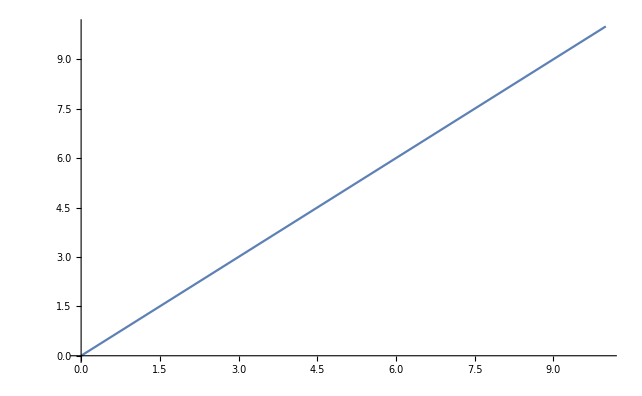

```mathematica
Show[%1,Background->White]
```

```mathematica
Plot[x,{x,0,10},PlotTheme->Automatic]
```

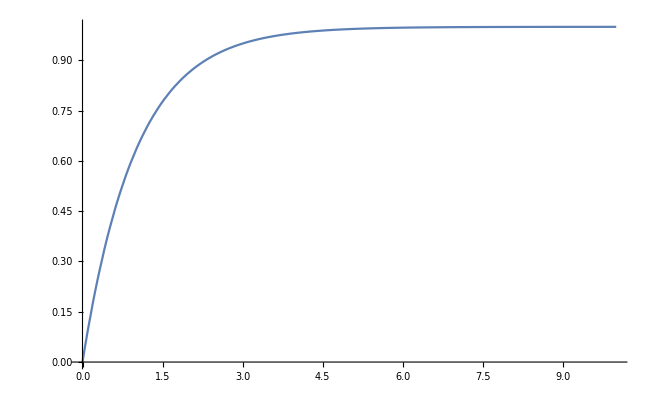

```mathematica
Show[%2,Background->White]
```

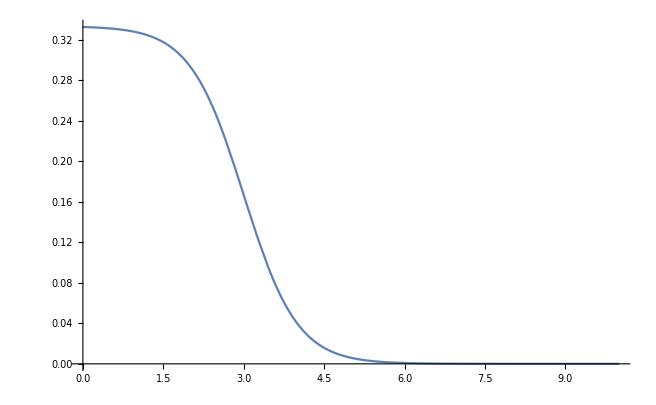

```mathematica
Show[%9,Background->White]
```

### hw2.m

### %% have MATLAB solve the equation

```mathematica
guess=0.332;
finalEta=5;%should be large when modifying the above value

f= @(t,x)[x(2);x(3);-x(1)*x(3)/2];
[etaa,soll]=ode45(f,[0,finalEta],[0,0,guess]);

soll(end,2) %check final f' value
```

### %% plots

```mathematica
close all
plot(etaa,soll(:,1))
xlabel('eta'),ylabel('f')
figure
plot(etaa,soll(:,2))
xlabel('eta'),ylabel('f prime')
figure
plot(etaa,soll(:,3))
xlabel('eta'),ylabel('f double prime')
```

### %% plots for comparison if hw2b.m has already been run

```mathematica
close all
figure('position',[0,0,1800,700])
subplot(1,3,1)
plot(etaa,soll(:,1),'k',eta,f1,'r')
xlabel('eta'),ylabel('f')
subplot(1,3,2)
plot(etaa,soll(:,2),'k',eta,f2,'r')
xlabel('eta'),ylabel('f prime')
subplot(1,3,3)
plot(etaa,soll(:,3),'k',eta,f3,'r')
xlabel('eta'),ylabel('f double prime')
```

### hw2b.m

```mathematica
stopEta=5;
pointsEta=51;
iterations=20;

h=stopEta/(pointsEta-1);% step size

eta=linspace(0,stopEta,pointsEta)';

% define our starting guesses (see Mathematica file for plots)
% you can verify the boundary conditions are true here
f1=eta;
f2=1-exp(-eta);
f3=(1-tanh(eta-3))/6;


for j=1:iterations

% evaluate our guesses/solutions at their centered values
halfF1=(f1(2:end)+f1(1:end-1))/2;
halfF2=(f2(2:end)+f2(1:end-1))/2;
halfF3=(f3(2:end)+f3(1:end-1))/2;

% loop over all points with equations to build up the matrix and b vector
% (see Mathematica file for the equations that gave us these)
matrix=[];
b=[];

for i=1:(pointsEta-1)
A=[-1/h,-1/2,0;0,-1/h,-1/2;halfF3(i)/4,0,halfF1(i)/4-1/h];
B=[1/h,-1/2,0;0,1/h,-1/2;halfF3(i)/4,0,halfF1(i)/4+1/h];
row=[repmat(zeros(3),1,i-1),A,B,repmat(zeros(3),1,pointsEta-1-i)];
matrix=[matrix;row];
b=[b;-(f1(i+1)-f1(i))/h+halfF2(i);-(f2(i+1)-f2(i))/h+halfF3(i);...-(f3(i+1)-f3(i))/h-halfF1(i)*halfF3(i)/2];
end

% add the final three rows to give boundary conditions
row1=zeros(1,pointsEta*3);
row2=zeros(1,pointsEta*3);
row3=zeros(1,pointsEta*3);
row1(1)=1;% df1(1)=0
row2(2)=1;% df2(1)=0
row3(end-1)=1;% df2(end)=0
b=[b;0;0;0];
matrix=[matrix;row1;row2;row3];

% solve the system
sol=matrix\b;
df1=sol(1:3:pointsEta*3);
df2=sol(2:3:pointsEta*3);
df3=sol(3:3:pointsEta*3);

% get new iteration
f1=f1+df1;
f2=f2+df2;
f3=f3+df3;

end

% sometimes round-off creeps in to give a negative value screwing up the
% plots...
f1(1)=0;
f2(1)=0;

% make plots
close all
figure('position',[0,0,1800,700])
subplot(1,3,1)
plot(eta,f1,'r')
xlabel('eta'),ylabel('f')
subplot(1,3,2)
plot(eta,f2,'r')
xlabel('eta'),ylabel('f prime')
subplot(1,3,3)
plot(eta,f3,'r')
xlabel('eta'),ylabel('f double prime')
```

### % red is the Keller Box Method (black is MATLAB’s solution)

Note: the only reason the black and the red plot lines vary seems to be because the MATLAB solver required an initial guess of f’’, hence what seems to be an overal scaling between the black and the red.

### blasius.f90 Fortran Code:

! use gfortran or gfortran-mp-5
! gfortran-mp-5 -c lu_solver.f90
! gfortran-mp-5 -o blasius blasius.f90 lu_solver.o 
! ./blasius
! gnuplot f.gpl 

program BLASIUS


use LU

implicit none

integer :: i,j,k,pointsETA,iterations
integer :: RC, d
real*8 :: stopETA, h ! real*8 double precision, 64 bit number (not 32 which is single)

parameter(pointsETA=31,stopETA=5.0,iterations=20)

real*8, dimension(pointsETA) :: eta,f1,f2,f3
real*8, dimension(pointsETA-1) :: halfF1,halfF2,halfF3
real*8, dimension(3*pointsETA) :: b ! breaking into a 3x3 system @ each point
integer, dimension(3*pointsETA) :: INDX
real*8, dimension(3*pointsETA,3*pointsETA) :: A


h = stopETA/(pointsETA-1.0) ! step size

do i=1,pointsETA
  eta(i) = (i-1)*h !(i-1) starts at zero
end do

! these are our initial guesses that satisfy the bcs
f1 = eta  ! this is f(eta)
f2 =1.0-exp(-eta)  ! this is f'(eta)
f3 =(1.0-tanh(eta -3.0))/6.0 ! this is f''(eta)


!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!
do j=1,iterations
do i=1,pointsETA-1 ! evaluate our guesses/solutions at their centered values
  halfF1(i) = ( f1(i+1)+f1(i) ) / 2.0
  halfF2(i) = ( f2(i+1)+f2(i) ) / 2.0
  halfF3(i) = ( f3(i+1)+f3(i) ) / 2.0
end do

A=0.0
b=0.0
do i=1, pointsETA-1
  k=(i-1)*3
  A( k+1, (/k+1,k+2,k+3,k+4,k+5,k+6/) ) = (/-1/h, -1/2.0d0, 0.0d0, 1/h, -1/2.0d0, 0.0d0/)

  A( k+2, (/k+1,k+2,k+3,k+4,k+5,k+6/) ) = (/0.0d0, -1/h, -1/2.0d0, 0.0d0,1/h, -1/2.0d0/)

  A( k+3,   (/k+1,k+2,k+3,k+4,k+5,k+6/) ) = (/halfF3(i)/4.0, 0.0d0, halfF1(i)/4.0-1/h, &
                                                halfF3(i)/4.0, 0.0d0, halfF1(i)/4.0+1/h/)

  b( (/k+1,k+2,k+3/) ) = (/ -(f1(i+1)-f1(i))/h +halfF2(i), -(f2(i+1)-f2(i))/h +halfF3(i), &
                      -( f3(i+1)-f3(i) )/h - halfF1(i)*halfF3(i)/2.0 /)
end do

! do the last 3 rows to assign bcs
k=pointsETA*3-3
A(k+1,1)=1 ! df1(1)=0
A(k+2,2)=1 ! df2(1)=0
A(k+3,pointsETA*3-1)=1 ! df2(pointsEta)=0


! take A and b and put solution into b
call LUDCMP(A, pointsETA*3,INDX,d,RC)
if (RC.eq.0) then
  call LUBKSB(A, pointsETA*3,INDX,b)
end if

do i=1,pointsETA
  k=(i-1)*3
  f1(i)=f1(i)+b(k+1)
  f2(i)=f2(i)+b(k+2)
  f3(i)=f3(i)+b(k+3)
end do

end do
!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!


! clean up round off error, to prevent negative values when plotting
f1(1)=0
f2(1)=0

102 FORMAT(f12.6,1x,f12.6,1x,f12.6,1x,f12.6)

! output with each value having its own line
open(1,file = 'f.dat', status = 'replace')
!write(1,*)'#    eta                  f1                    f2                    f3'
write(1,*)'#    eta          f1          f2            f3'
do i = 1, pointsETA
  write(1,102) eta(i),f1(i),f2(i),f3(i)
end do


end program

### lu_solver.f90 LU-decomposition

!*******************************************************
!*    LU decomposition routines used by test_lu.f90    *
!*                                                     *
!*                 F90 version by J-P Moreau, Paris    *
!* --------------------------------------------------- *
!* Reference:                                          *
!*                                                     *
!* "Numerical Recipes By W.H. Press, B. P. Flannery,   *
!*  S.A. Teukolsky and W.T. Vetterling, Cambridge      *
!*  University Press, 1986" [BIBLI 08].                *
!*                                                     * 
!*******************************************************
MODULE LU
CONTAINS

    !  ***************************************************************
    !  * Given an N x N matrix A, this routine replaces it by the LU *
    !  * decomposition of a rowwise permutation of itself. A and N   *
    !  * are input. INDX is an output vector which records the row   *
    !  * permutation effected by the partial pivoting; D is output   *
    !  * as -1 or 1, depending on whether the number of row inter-   *
    !  * changes was even or odd, respectively. This routine is used *
    !  * in combination with LUBKSB to solve linear equations or to  *
    !  * invert a matrix. Return code is 1, if matrix is singular.   *
    !  ***************************************************************
     Subroutine LUDCMP(A,N,INDX,D,CODE)
     IMPLICIT NONE
     integer, parameter :: nmax = 100
     real, parameter :: tiny = 1.5D-16

     real*8, intent(inout), dimension(N,N) :: A
     integer, intent(in) :: N
     integer, intent(out) :: D, CODE
     integer, intent(out), dimension(N) :: INDX
     !f2py depend(N) A, indx

     REAL*8  :: AMAX, DUM, SUMM, VV(NMAX)
     INTEGER :: i, j, k, imax

     D=1; CODE=0

     DO I=1,N
       AMAX=0.d0
       DO J=1,N
         IF (DABS(A(I,J)).GT.AMAX) AMAX=DABS(A(I,J))
       END DO ! j loop
       IF(AMAX.LT.TINY) THEN
         CODE = 1
         RETURN
       END IF
       VV(I) = 1.d0 / AMAX
     END DO ! i loop

     DO J=1,N
       DO I=1,J-1
         SUMM = A(I,J)
         DO K=1,I-1
           SUMM = SUMM - A(I,K)*A(K,J) 
         END DO ! k loop
         A(I,J) = SUMM
       END DO ! i loop
       AMAX = 0.d0
       DO I=J,N
         SUMM = A(I,J)
         DO K=1,J-1
           SUMM = SUMM - A(I,K)*A(K,J) 
         END DO ! k loop
         A(I,J) = SUMM
         DUM = VV(I)*DABS(SUMM)
         IF(DUM.GE.AMAX) THEN
           IMAX = I
           AMAX = DUM
         END IF
       END DO ! i loop  
       
       IF(J.NE.IMAX) THEN
         DO K=1,N
           DUM = A(IMAX,K)
           A(IMAX,K) = A(J,K)
           A(J,K) = DUM
         END DO ! k loop
         D = -D
         VV(IMAX) = VV(J)
       END IF

       INDX(J) = IMAX
       IF(DABS(A(J,J)) < TINY) A(J,J) = TINY

       IF(J.NE.N) THEN
         DUM = 1.d0 / A(J,J)
         DO I=J+1,N
           A(I,J) = A(I,J)*DUM
         END DO ! i loop
       END IF 
     END DO ! j loop

     RETURN
 END subroutine LUDCMP


!  ******************************************************************
!  * Solves the set of N linear equations A . X = B.  Here A is     *
!  * input, not as the matrix A but rather as its LU decomposition, *
!  * determined by the routine LUDCMP. INDX is input as the permuta-*
!  * tion vector returned by LUDCMP. B is input as the right-hand   *
!  * side vector B, and returns with the solution vector X. A, N and*
!  * INDX are not modified by this routine and can be used for suc- *
!  * cessive calls with different right-hand sides. This routine is *
!  * also efficient for plain matrix inversion.                     *
!  ******************************************************************
 Subroutine LUBKSB(A, N, INDX, B)
 integer, intent(in) :: N 
 real*8, intent(in), dimension(N,N) :: A
 integer, intent(in), dimension(N) :: INDX
 real*8, intent(inout), dimension(N) :: B
 !f2py depend(N) A, INDX, B

 REAL*8  SUMM

 II = 0

 DO I=1,N
   LL = INDX(I)
   SUMM = B(LL)
   B(LL) = B(I)
   IF(II.NE.0) THEN
     DO J=II,I-1
       SUMM = SUMM - A(I,J)*B(J)
     END DO ! j loop
   ELSE IF(SUMM.NE.0.d0) THEN
     II = I
   END IF
   B(I) = SUMM
 END DO ! i loop

 DO I=N,1,-1
   SUMM = B(I)
   IF(I < N) THEN
     DO J=I+1,N
       SUMM = SUMM - A(I,J)*B(J)
     END DO ! j loop
   END IF
   B(I) = SUMM / A(I,I)
 END DO ! i loop

 RETURN
 END subroutine LUBKSB

END MODULE LU

### f.gpl (for data files and gnuplot)

#### run with `gnuplot f.gpl`

set xlabel 'eta'

####do the following to create a PNG
set terminal png

set ylabel 'f'
set output "f1.png"
plot "f.dat" using 1:2 with lines title ''
set ylabel "f '"
set output "f2.png"
plot "f.dat" using 1:3 with lines title ''
set ylabel "f ''"
set output "f3.png"
plot "f.dat" using 1:4 with lines title ''

### f.dat (data file)

#    eta          f1          f2            f3
    0.000000     0.000000     0.000000     0.333219
    0.166667     0.004628     0.055531     0.333155
    0.333333     0.018508     0.111030     0.332834
    0.500000     0.041630     0.166433     0.332001
    0.666667     0.073968     0.221633     0.330405
    0.833333     0.115478     0.276485     0.327807
    1.000000     0.166085     0.330800     0.323984
    1.166667     0.225682     0.384361     0.318738
    1.333333     0.294122     0.436915     0.311909
    1.500000     0.371214     0.488189     0.303380
    1.666667     0.456721     0.537895     0.293092
    1.833333     0.550357     0.585740     0.281046
    2.000000     0.651788     0.631436     0.267313
    2.166667     0.760634     0.674715     0.252031
    2.333333     0.876472     0.715334     0.235406
    2.500000     0.998841     0.753094     0.217703
    2.666667     1.127252     0.787839     0.199236
    2.833333     1.261194     0.819470     0.180348
    3.000000     1.400146     0.847949     0.161400
    3.166667     1.543583     0.873295     0.142747
    3.333333     1.690989     0.895584     0.124723
    3.500000     1.841867     0.914946     0.107622
    3.666667     1.995742     0.931556     0.091687
    3.833333     2.152173     0.945621     0.077102
    4.000000     2.310757     0.957378     0.063984
    4.166667     2.471128     0.967076     0.052390
    4.333333     2.632965     0.974969     0.042319
    4.500000     2.795988     0.981305     0.033719
    4.666667     2.959957     0.986323     0.026498
    4.833333     3.124671     0.990243     0.020536
    5.000000     3.289963     0.993262     0.015694

### Fortran Plots

## Part 3: Spectral Collocation Method (in progress)

3A)

Mathematica Code:

```mathematica
OrrSSolv[Np_,Rey_,α_] := Module[{d,Dmatrix,D2,D3,D4,D2a,D3a,D4a,diag1,diag2,diag3,S,diag4,A,A1,B,B1,y},
(*housam diff matrix*)
d[0,0]=(2Np^2+1)/6//N;
  d[Np,Np]=-(2Np^2+1)/6//N;
y[i_]:=Cos[i Pi/Np]//N;
d[i_,i_]:=-y[i]/(2(1-y[i]^2))//N;
  d[j_,k_]:=
If[j≠k&&k≠0&&k≠Np&&j≠0&&j≠Np,(-1)^(j+k)/(y[j]-y[k])]//N;
	d[Np,0]=-1/2(-1)^Np;
	d[0,Np]=1/2(-1)^Np;
d[j_,0]:=If[j≠Np&&j≠0,-1/2(-1)^j/(1-y[j])];
d[j_,Np]:=If[j≠Np&&j≠0,1/2(-1)^(j+Np)/(1+y[j])];
d[0,j_]:=If[j≠Np&&j≠0,2(-1)^j/(1-y[j])];	
d[Np,j_]:=If[j≠Np&&j≠0,-2(-1)^(j+Np)/(1+y[j])];
Dmatrix=Table[d[i,j],{i,0,Np},{j,0,Np}];
(*make/gen the diff matrices*)
D2=Dmatrix.Dmatrix;
D3=Dmatrix.Dmatrix.Dmatrix;
D4=Dmatrix.Dmatrix.Dmatrix.Dmatrix;
(*make/gen the diag elem for all the diag matrices*)
diag1=Table[1-N[Cos[i*Pi/Np]]^2,{i,0,Np}];
diag2 =Table[N[Cos[i Pi/Np]],{i,0,Np}];
diag3=Join[{0},Table[1/(1-N[Cos[i Pi/Np]^2]),{i,1,Np-1}],{0}];
S=DiagonalMatrix[diag3];
(*make/assemble matrices A and B for the gen eig-value problem:A·U=λB·U*)
A=Rey^-1((DiagonalMatrix[diag1].D4-8DiagonalMatrix[diag2].D3-12D2).S-2 α^2 D2+α^4 IdentityMatrix[Np+1])-2α I IdentityMatrix[Np+1]-I α  DiagonalMatrix[diag1].(D2-IdentityMatrix[Np+1]);
B=(D2-α^2 IdentityMatrix[Np+1]);
(*Because of the BCs chosen:q(-1)=0,q(1)=0 we delete the first and last
rows and its first and last columns of the A and B matrices. *)
A1=A[[2;;Np,2;;Np]];
B1=B[[2;;Np,2;;Np]];
(*Next we solve the generalized eigenvalue problem*)
res=Reverse[Eigenvalues[{A1,B1}]];
ListPlot[res/.Complex[a_,b_]->{a,b},Frame->True,PlotRange->{{0.5,-2},{0.0,-1.0}},FrameLabel->{Style["Re(λ)",18],Style["Im(λ)",18]},PlotLabel->"Most Problematic mode:\n λ="<> ToString[NumberForm[res[[1]],NumberFormat->(Row[{#1,"e",#3}]&)]]]
]
```

3B)

```mathematica
Using Subscript[α, crit]=1.02056, Re=5772.22 from  S. A. Orszag, Accurate solution of the Orr-Sommerfeld stability equation, J. Fluid Mech., 50,
pp. 689-703, (1971)
```

### Below Re=5777.2, @ α_crit flow unstable.

```mathematica
OrrSSolv[100,6000,1.02056]
```

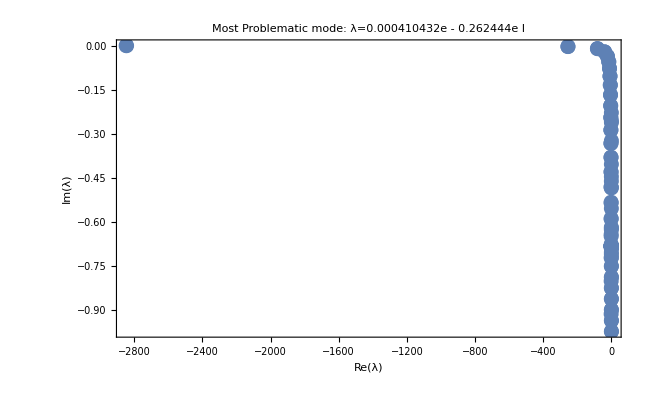

### Below calc is @ α_crit however Re<Re_crit=5772.22. Flow stable.

```mathematica
OrrSSolv[100,5770,1.02056]
```

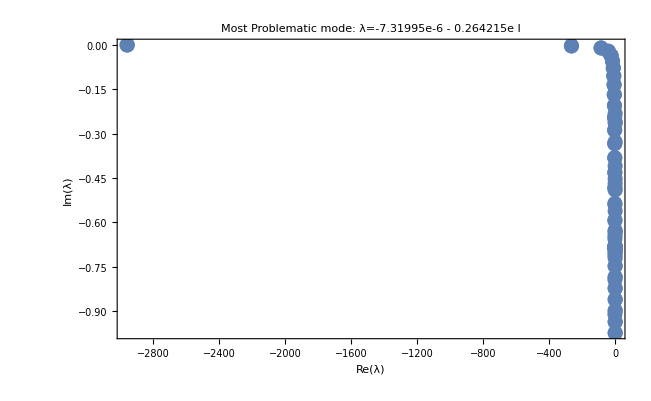

### Below from Orszag reference table, all values in the plot are below “Most Problematic Mode” agree identical to that of Orszag reference using ~50 Chebyshev polynomials.

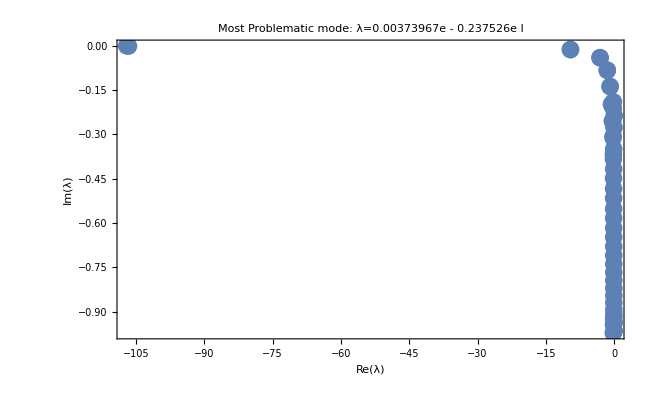

```mathematica
OrrSSolv[50,10000,1]
```